## 計算結果

```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../../mathematica_plot_options.nb"}]]
(*json="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.json"*)
(*json ="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water_no_float0d09/result.json"*)
jsonTarget=json="/Users/tomoaki/BEM/Tanizawa1996_DT0d05_ELEMlinear_ALEpseudo_quad_ALEPERIOD1/result.json"
jsonInfo[json]
```

{plot2Doption,plot3Doption,framelabel[xlabel_String,ylabel_String,size_:20],axeslabel2D[xlabel_String,ylabel_String,size_:20],axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20],axeslabel[labels_List,size_: 20],importData,jsonInfo,interpolateAndFourier[time_List,disp_List,timeSpan_List: {}],interpolateAndFourierTr[timedisp_List,timeSpan_List: {}],MyFourier[list_,n_],MyInverseFourier[list_,n_],MyDiscreteConvolve[f_,g_],MyDiscreteConvolveUsingCn[FourierGF_],Rv[q_],Rs[q_],W2dQdt[q_,w_],Q2Roll[{a_,b_,c_,d_}],Q2Pitch[{a_,b_,c_,d_}],Q2Yaw[{a_,b_,c_,d_}],getOmegaFromKandDepth[k_,h_],getOmegaFromLandDepth[L_,h_],getTFromLandDepth[L_,h_],getkFromTandDepth[T_,h_]}

/Users/tomoaki/BEM/Tanizawa1996_DT0d05_ELEMlinear_ALEpseudo_quad_ALEPERIOD1/result.json

no. | title | length
1 | cpu_time | 1254
2 | eq_of_motion | 1254
3 | float_COM | 1254
4 | float_EK | 1254
5 | float_EP | 1254
6 | float_accel | 1254
7 | float_area | 1254
8 | float_drag_force | 1254
9 | float_drag_torque | 1254
10 | float_force | 1254
11 | float_pitch | 1254
12 | float_roll | 1254
13 | float_torque | 1254
14 | float_velocity | 1254
15 | float_yaw | 1254
16 | gauge0_intersection | 1254
17 | gauge1_intersection | 1254
18 | gauge2_intersection | 1254
19 | gauge3_intersection | 1254
20 | gauge4_intersection | 1254
21 | gauge5_intersection | 1254
22 | gauge6_intersection | 1254
23 | gauge7_intersection | 1254
24 | gauge8_intersection | 1254
25 | gauge9_intersection | 1254
26 | gradPhi_worst_grad | 1254
27 | gradPhi_worst_iteration | 1254
28 | gradPhi_worst_value | 1254
29 | simulation_time | 1254
30 | wall_clock_time | 1254
31 | water_E | 1254
32 | water_EK | 1254
33 | water_EP | 1254
34 | water_face_size | 1254
35 | water_point_size | 1254
36 | water_volume | 1254

```mathematica
(*i=1;
ListPlot[
Table[With[{name="float"<>ToString[i]<>"_COM"},importData[json,name,1]-importData[json,name,1][[1]]],{i,1,20,1}]
,Joined->True
]
ListPlot[
Table[With[{name="float"<>ToString[i]<>"_COM"},importData[json,name,2]-importData[json,name,2][[1]]],{i,1,20,1}]
,Joined->True
]
ListPlot[
Table[With[{name="float"<>ToString[i]<>"_COM"},importData[json,name,3]-importData[json,name,3][[1]]],{i,1,20,1}]
,Joined->True
]*)
```

```mathematica
(*Tshift=6.5*)
```

```mathematica
ζa=0.05/2;
(*{B,L}={0.74,0.997};(*{Bredth,Length}*)*)
{B,L}={0.74,1};(*{Bredth,Length}*)
g=9.8;
ρ=1000;
λ=1.8;
ρgLBζa=ρ*g*L*B*ζa

h=4.5;
Omega[k_,h_]:=Sqrt[g*k*Tanh[h*k]];
Tw=T/.Solve[Omega[2π/λ,h]==2π/T,T][[1]]

k=2π/L;
ω=Omega[k,h];


Tshift=1.074269
ExpHeave={Tw*#1-Tshift,ζa*#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_heave_exp.csv"];
SimuHeave={Tw*#1-Tshift,ζa*#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_heave_simu.csv"];
ExpSway={Tw*#1-Tshift,ζa*#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_sway_exp.csv"];
SimuSway={Tw*#1-Tshift,ζa*#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_sway_simu.csv"];
ExpRoll={Tw*#1-Tshift,k*ζa*#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_roll_exp.csv"];
SimuRoll={Tw*#1-Tshift,k*ζa*#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_roll_simu.csv"];
ExpSf={Tw*#1-Tshift,ρgLBζa*#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Sf_exp.csv"];
SimuSf={Tw*#1-Tshift,ρgLBζa*#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Sf_simu.csv"];
SimuRm={Tw*#1-Tshift,ρgLBζa*B*#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Rm_simu.csv"];
SimuHf={Tw*#1-Tshift,ρgLBζa*#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Hf_simu.csv"];
```

181.3

Solve::ratnz: Solveは厳密でない係数の系を解くことができませんでした．解は対応する厳密系を解き，結果を数値に変換することで得られました．

1.07427

1.07427

## 計算結果

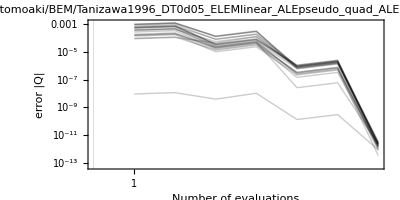

```mathematica
fourColorScheme={
{Thick,Opacity[0.8],Blue(*RGBColor[55/255,126/255,184/255]*)},
{Thickness[0.002],Opacity[0.8],Red(*RGBColor[255/255,127/255,0]*)},
{Thickness[0.002],RGBColor[77/255,175/255,74/255]},
{Thickness[0.002],RGBColor[247/255,129/255,191/255]}};
threeColorScheme={{Thick,RGBColor[55/255,126/255,184/255]},RGBColor[255/255,127/255,0],RGBColor[77/255,175/255,74/255]};
plotxrange={{0,30},All};
opt={FrameStyle->Directive[FontSize->16,Black,Thickness[0.002]],
Epilog->{Line[{{-100,0},{100,0}}]},
Joined->{True,True,True,False},
PlotRange->plotxrange,
GridLines->All,
GridLinesStyle->Directive[Gray,AbsoluteThickness[0.001]],
ImageSize->1000,
PlotStyle->{{Blue},{Red},{Darker[Green]}},
PlotStyle->fourColorScheme,
AspectRatio->1/8};
(*メッシュと計算の収束*)
(*プロット*)
Column@Table[
data=importData[json,"eq_of_motion"];
ListLogPlot[Table[Transpose@{Range[Length[data[[i]]]],data[[i]]},{i,1,20}],
PlotLabel->json,
PlotRange->Automatic,
PlotStyle->Directive[Thin,Black,Opacity[0.2]],
FrameTicks->{{All,Automatic},{Table[i,{i,1,100,1}],None}},
AspectRatio->1/2,
FrameLabel->{
Style["Number of evaluations",FontSize->20,FontFamily->"Times"],
Rotate[Style["error |Q|",FontSize->20,FontFamily->"Times"],-π/2]},
Frame->True,
Evaluate[plot2Doption]
],{json,
{json=jsonTarget(*,
"/Volumes/home/BEM/20240301土木学会東北支部/Tanizawa1996_H0d05_L1d8_potential_multiple_water_mod_coarse/result.json"*)}}]
```

この計算条件では，準ニュートン法の繰り返し計算7回で | Q | < 10^-12 にまで収束した．
浮体を増やすと，収束の速さは遅くなるものの収束する．

```mathematica
opt=Prepend[opt,{
PlotLegends->Placed[{"Present","Numerical (Tanizawa, 1997)","Experimental (Tanizawa, 1997)"},Right],
PlotRange->{All,Automatic}
}];
```

25

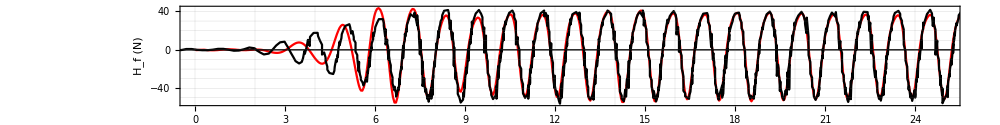

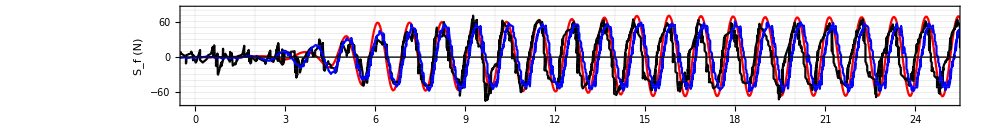

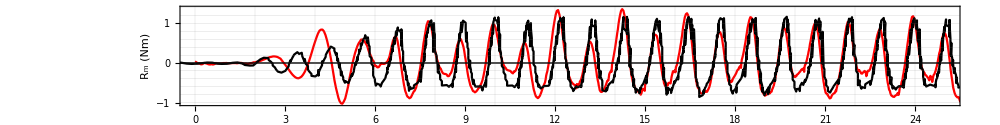

```mathematica
endt=25
ListPlot[
{
{importData[json,"simulation_time"],importData[json,"float_force",3]-importData[json,"float_force",3][[5]]}ᵀ,
SimuHf},
PlotStyle->{Red,Black,Blue},
PlotRange->{{0,endt},All},
Evaluate[opt],
FrameLabel->{Style["t (s)",FontSize->20,FontFamily->"Times"],Style["H_f (N)",FontSize->20,FontFamily->"Times"]},
PlotLegends->{"x","y","z"},
Evaluate[plot2Doption]
]

ListPlot[
{
{importData[json,"simulation_time"],importData[json,"float_force",1]-importData[json,"float_force",1][[5]]}ᵀ,
ExpSf,
SimuSf
},
PlotStyle->{Red,Black,Blue},
PlotRange->{{0,endt},All},
Evaluate[opt],
FrameLabel->{Style["t (s)",FontSize->20,FontFamily->"Times"],Style["S_f (N)",FontSize->20,FontFamily->"Times"]},
PlotLegends->{"x","y","z"},
Evaluate[plot2Doption]
]

ListPlot[
{
{importData[json,"simulation_time"],-(importData[json,"float_torque",2]-importData[json,"float_torque",2][[15]])}ᵀ,
SimuRm
},
PlotStyle->{Red,Black,Blue},
PlotRange->{{0,endt},All},
Evaluate[opt],
FrameLabel->{Style["t (s)",FontSize->20,FontFamily->"Times"],Style["R_m (Nm)",FontSize->20,FontFamily->"Times"]},
PlotLegends->{"x","y","z"},
Evaluate[plot2Doption]
]
```

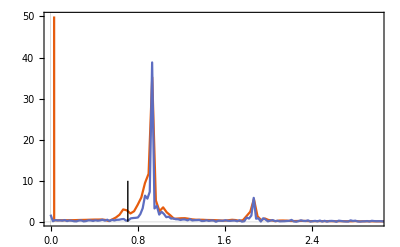

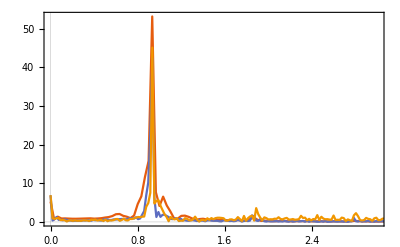

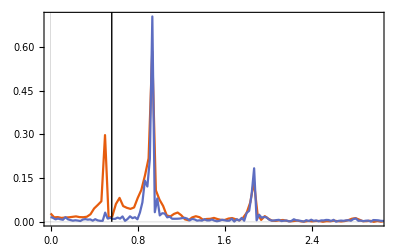

```mathematica
ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"],importData[json,"float_force",3]],
interpolateAndFourier[SimuHf[[;;,1]],SimuHf[[;;,2]]]
},
PlotRange->{{0,3},{0,50}},
Epilog->Line[{{1/1.41,0},{1/1.41,10}}],
Evaluate[plot2Doption]
]

ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"],importData[json,"float_force",1]]
,interpolateAndFourier[SimuSf[[;;,1]],SimuSf[[;;,2]]]
,interpolateAndFourier[ExpSf[[;;,1]],ExpSf[[;;,2]]]
},
PlotRange->{{0,3},All},
Evaluate[plot2Doption]
]

ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"],importData[json,"float_torque",2]],
interpolateAndFourier[SimuRm[[;;,1]],SimuRm[[;;,2]]]
},
Epilog->Line[{{1/1.78,0},{1/1.78,10}}],
PlotRange->{{0,3},All},
Evaluate[plot2Doption]
]
```

浮体が流体から受ける，鉛直水平方向の力，y軸回転方向のトルクは，Tanizawa1997の結果とよく一致している．

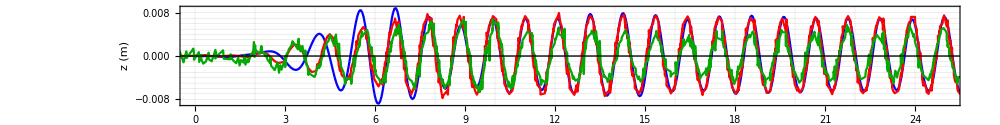

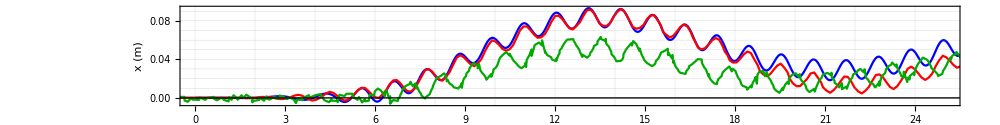

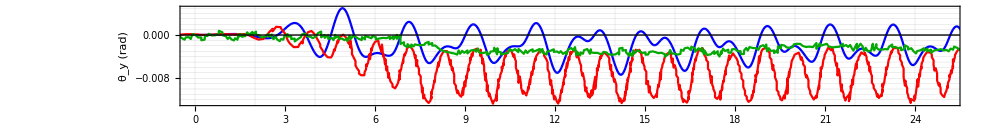

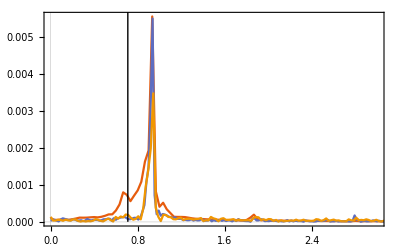

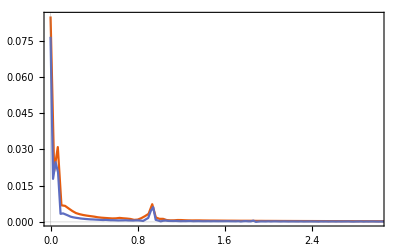

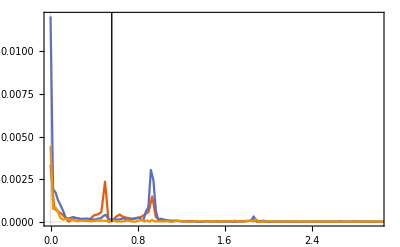

```mathematica
ListPlot[
{{importData[json,"simulation_time"],(importData[json,"float_COM",3]-importData[json,"float_COM",3][[1]])}ᵀ,
SimuHeave,
ExpHeave},
PlotRange->{{0,endt},All},
Evaluate[opt],
FrameLabel->{Style["t (s)",FontSize->20,FontFamily->"Times"],Style["z (m)",FontSize->20,FontFamily->"Times"]},
(*PlotLabel->"heave",*)
Evaluate[plot2Doption]
]
Export[FileNameJoin[{NotebookDirectory[],"heave.eps"}],%];

ListPlot[
{{importData[json,"simulation_time"],(importData[json,"float_COM",1]-importData[json,"float_COM",1][[1]])}ᵀ,
SimuSway,
ExpSway},
PlotRange->{{0,endt},All},
Evaluate[opt],
GridLines->{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]},
FrameLabel->{Style["t (s)",FontSize->20,FontFamily->"Times"],Style["x (m)",FontSize->20,FontFamily->"Times"]},
(*PlotLabel->"surge",*)
Evaluate[plot2Doption]
]
Export[FileNameJoin[{NotebookDirectory[],"surge.eps"}],%];

k=2π/λ;
ListPlot[
{{importData[json,"simulation_time"],-(importData[json,"float_pitch"])}ᵀ,
SimuRoll,
ExpRoll},
PlotRange->{{0,endt},All},
Evaluate[opt],
FrameLabel->{Style["t (s)",FontSize->20,FontFamily->"Times"],Style["θ_y (rad)",FontSize->20,FontFamily->"Times"]},
Evaluate[plot2Doption]
]
Export[FileNameJoin[{NotebookDirectory[],"pitch.eps"}],%];

ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"],(importData[json,"float_COM",3]-importData[json,"float_COM",3][[1]])]
,interpolateAndFourier[SimuHeave[[;;,1]],SimuHeave[[;;,2]]]
,interpolateAndFourier[ExpHeave[[;;,1]],ExpHeave[[;;,2]]]
},
PlotRange->{{0,3},All},
Epilog->Line[{{1/1.41,0},{1/1.41,10}}],
Evaluate[plot2Doption]
]

ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"],(importData[json,"float_COM",1]-importData[json,"float_COM",1][[1]])]
,interpolateAndFourier[SimuSway[[;;,1]],SimuSway[[;;,2]]]
},
PlotRange->{{0,3},All},
Evaluate[plot2Doption]
]

ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"],-(importData[json,"float_pitch"])]
,interpolateAndFourier[SimuRoll[[;;,1]],SimuRoll[[;;,2]]]
,interpolateAndFourier[ExpRoll[[;;,1]],ExpRoll[[;;,2]]]
},
Epilog->Line[{{1/1.78,0},{1/1.78,10}}],
PlotRange->{{0,3},All},
Evaluate[plot2Doption]
]
```

ロール角を除き，浮体の並進移動は，Tanizawa1997の計算結果とよく一致している．一方の回転角度は，谷澤の結果よりも小さく

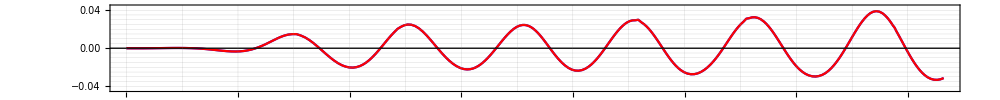
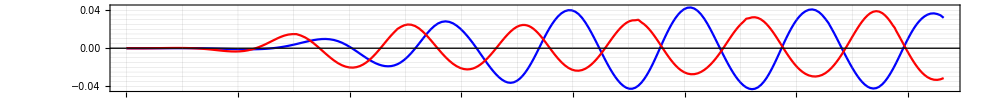
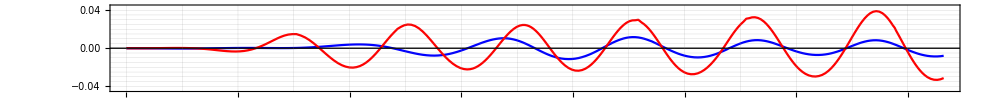
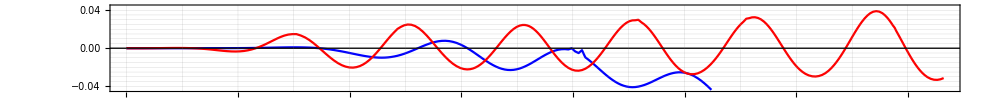
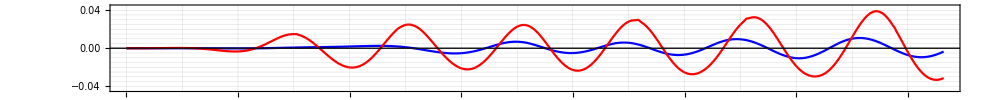
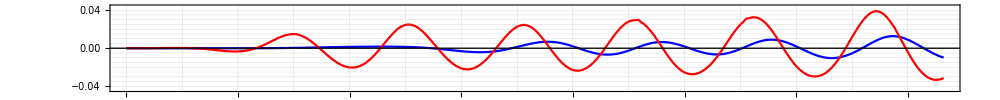
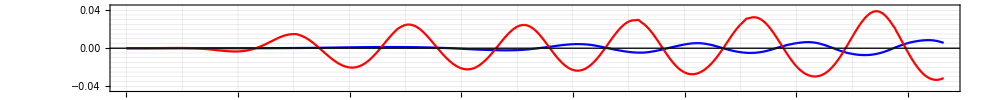
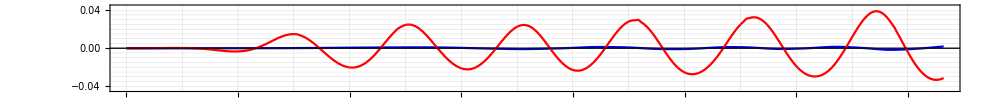
-Graphics--1.15
-Graphics--0.65
-Graphics-0.01875
-Graphics-0.37
-Graphics-0.85
-Graphics-1.35
-Graphics-1.85
-Graphics-2.35
-Graphics-2.85
-Graphics-100000000000000000000

```mathematica
delt=0.67/(ω/k);
T=1.;
DATA1=importData[json,"gauge0_intersection",3];
Column[Table[
Module[{data,DATA,position},
data="gauge"<>ToString[i]<>"_intersection";
DATA=importData[json,data,3];
position=importData[json,data,1][[1]];
Labeled[
ListPlot[
{{importData[json,"simulation_time"],(DATA-DATA[[1]])}ᵀ,
{importData[json,"simulation_time"](*+(*0.295*)delt*i*),(DATA1-DATA1[[1]])}ᵀ
(*Table[{t,-ζa*Cos[2π/T*t-k*(position)]},{t,0,30,.1}]*)
},
(*FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/H_0",FontSize->20,FontFamily->"Times",Italic]},*)
AspectRatio->1/10,
PlotRange->{Automatic,1.75*{-ζa,ζa}},
Joined->{True,True,True,True,True},
Evaluate[opt],
(*PlotStyle->plotstyle,*)
Evaluate[plot2Doption]
]
,position
,Right]
],{i,0,9,1}]
,Spacings->0
]
```

```mathematica
(*Mock-up for demonstration:Generates sample data similar to your structure*)
sampleData=Table[
Module[{data,DATA,position,w,v,fourier},
data="gauge"<>ToString[i]<>"_intersection";
DATA=importData[json,data,3];
position=importData[json,data,1][[1]];
{w,v}=Transpose[interpolateAndFourierTr[{importData[json,"simulation_time"],(DATA-DATA[[1]])}ᵀ,{10,15}]];
Transpose[{Table[i,{j,1,Length[w]}],w,v}]
],{i,1,9,1}];

minmax=MinMax[#3&@@@Flatten[sampleData,1]];

(*Visualization code*)
Graphics3D[Table[{ColorData["BlueGreenYellow"][sampleData[[i,j,3]]/minmax[[2]]],
Cuboid[{
sampleData[[i,j,1]],
sampleData[[i,j,2]],0},
{sampleData[[i,j,1]]+0.8,sampleData[[i,j,2]]+0.095,sampleData[[i,j,3]]}]},
{i,1,Length[sampleData]},{j,1,Length[sampleData[[i]]]}],Axes->True,BoxRatios->{1,1,1/2},PlotRange->{All,{0,3},All}]
```

Set::shape: {w$134012,v$134012}と{}のリストは型が違います．

Transpose::nmtx: {{},w$134012,v$134012}の最初の2個のレベルは転置できません．

Set::shape: {w$134128,v$134128}と{}のリストは型が違います．

Transpose::nmtx: {{},w$134128,v$134128}の最初の2個のレベルは転置できません．

Set::shape: {w$134244,v$134244}と{}のリストは型が違います．

General::stop: この計算中に，Set::shapeのこれ以上の出力は表示されません．

Transpose::nmtx: {{},w$134244,v$134244}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

Function::slotn: #3&のスロット番号3を(#3&)[{{},w$134012,v$134012}]から満たすことができません．

Function::slotn: #3&のスロット番号3を(#3&)[{{},w$134128,v$134128}]から満たすことができません．

Function::slotn: #3&のスロット番号3を(#3&)[{{},w$134244,v$134244}]から満たすことができません．

General::stop: この計算中に，Function::slotnのこれ以上の出力は表示されません．

-Graphics3D-

## 収束性のチェック

```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../../mathematica_plot_options.nb"}]]
json="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json"
jsonInfo[json]
plotstyle=Table[RGBColor[{Sin[i*π]/2+1/2,Cos[i*π]/2+1/2,i}],{i,0,1,0.2}]
rbgs=Table["#"<>StringJoin[IntegerString[Round[#],16,2]&/@({255*Sin[i*π]/2+1/2,Cos[i*π]/2+1/2,i})],{i,0,1,0.2}]
hexColor="#"<>StringJoin[IntegerString[#,16,2]&/@rbgs[[1]]]


legend={(*"0.1",*)"0.09","0.08","0.07","0.06","0.05"}
```

{plot2Doption,plot3Doption,framelabel[xlabel_String,ylabel_String,size_:20],axeslabel2D[xlabel_String,ylabel_String,size_:20],axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20],axeslabel[labels_List,size_: 20],importData,jsonInfo,interpolateAndFourier[time_List,disp_List,timeSpan_List: {}],interpolateAndFourierTr[timedisp_List,timeSpan_List: {}],MyFourier[list_,n_],MyInverseFourier[list_,n_],MyDiscreteConvolve[f_,g_],MyDiscreteConvolveUsingCn[FourierGF_],Rv[q_],Rs[q_],W2dQdt[q_,w_],Q2Roll[{a_,b_,c_,d_}],Q2Pitch[{a_,b_,c_,d_}],Q2Yaw[{a_,b_,c_,d_}],getOmegaFromKandDepth[k_,h_],getOmegaFromLandDepth[L_,h_],getTFromLandDepth[L_,h_],getkFromTandDepth[T_,h_]}

/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.jsonが見付かりませんでした．

no. | title | length

{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]}

{#000100,#4b0100,#7a0100,#7a0001,#4b0001,#010001}

##000100

{0.09,0.08,0.07,0.06,0.05}

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Part::partw: (float_COM/.$Failed)⟦1;;All,3⟧の部分250は存在しません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

Part::partw: (float_COM/.$Failed)⟦1;;All,3⟧の部分250は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

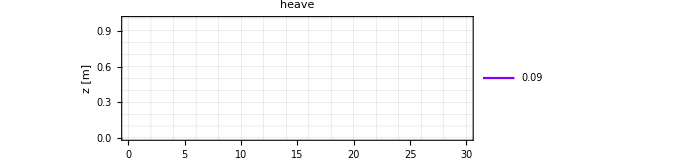

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

Part::partw: (float_COM/.$Failed)⟦1;;All,1⟧の部分250は存在しません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

Part::partw: (float_COM/.$Failed)⟦1;;All,1⟧の部分250は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

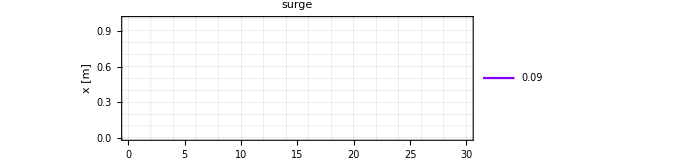

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partw: float_pitch/.$Failedの部分250は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

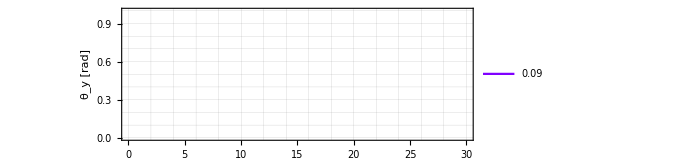

```mathematica
jsons={(*"/Volumes/home/BEM/20240301土木学会東北支部/Tanizawa1996_H0d05_L1d8_potential_water_mod_0d1/result.json",*)
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d08/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d07/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d05/result.json"(*,
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_3/result.json"*)};

plotxrange={{0,30},All};
opt2={FrameStyle->Directive[FontSize->16,Black,Thickness[0.002]],
PlotStyle->plotstyle,
Joined->{True,True,True,True},
PlotRange->plotxrange,
GridLines->All,
GridLinesStyle->Directive[Gray,AbsoluteThickness[0.001]],
ImageSize->500,
(*PlotStyle->{{Darker[Blue,0.1]},{Darker[Blue,0.3]},{Darker[Blue,0.6]},{Darker[Blue,0.9]}},*)
AspectRatio->1/3};
(*メッシュと計算の収束*)

fig=ListPlot[
Table[{importData[jsons[[i]],"simulation_time"],(importData[jsons[[i]],"float_COM",3]-importData[jsons[[i]],"float_COM",3][[250]])}ᵀ,
{i,1,Length[jsons]}],
PlotStyle->plotstyle,
Evaluate[opt2],
(*PlotRange->{{0,12.},{-0.07,0.07}},*)
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["z [m]",FontSize->20,FontFamily->"Times"]},
PlotLegends->legend,
PlotLabel->"heave",
Evaluate[plot2Doption]
]
ListPlot[
Table[{importData[jsons[[i]],"simulation_time"],(importData[jsons[[i]],"float_COM",1]-importData[jsons[[i]],"float_COM",1][[250]])}ᵀ,{i,1,Length[jsons]}],
PlotStyle->plotstyle,
Evaluate[opt2],
PlotRange->{All,Automatic},
GridLines->{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x [m]",FontSize->20,FontFamily->"Times"]},
PlotLegends->legend,
PlotLabel->"surge",
Evaluate[plot2Doption]
]
k=2π/λ;
ListPlot[
Table[{importData[jsons[[i]],"simulation_time"],-(importData[jsons[[i]],"float_pitch"]-importData[jsons[[i]],"float_pitch"][[250]])}ᵀ,{i,1,Length[jsons]}],
PlotStyle->plotstyle,
Evaluate[opt2],
PlotLegends->legend,
PlotRange->{All,All},
PlotRange->{Automatic,Automatic},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["θ_y [rad]",FontSize->20,FontFamily->"Times"]},
Evaluate[plot2Doption]
]
```

```mathematica
json1="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water_no_float0d09/result.json"
delt=0.67/(ω/k);
T=1.;
DATA1=importData[json1,"gauge0_intersection",3];
Column[ParallelTable[
Module[{data,DATA,position},
data="gauge"<>ToString[i]<>"_intersection";
DATA=importData[json,data,3];
position=importData[json,data,1][[1]];
Labeled[
ListPlot[
{{importData[json,"simulation_time"],(DATA-DATA[[1]])}ᵀ,
{importData[json,"simulation_time"](*+(*0.295*)delt*i*),(DATA1-DATA1[[1]])}ᵀ
(*Table[{t,-ζa*Cos[2π/T*t-k*(position)]},{t,0,30,.1}]*)
},
(*FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/H_0",FontSize->20,FontFamily->"Times",Italic]},*)
AspectRatio->1/10,
PlotRange->{Automatic,1.75*{-ζa,ζa}},
Joined->{True,True,True,True,True},
Evaluate[opt],
PlotStyle->plotstyle,
Evaluate[plot2Doption]
]
,position
,Right]
],{i,0,23,1}]
,Spacings->0
]
```

/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water_no_float0d09/result.json

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water_no_float0d09/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(gauge0_intersection/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json not found during Import.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json not found during Import.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification (gauge19_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification (gauge0_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge1_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge2_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge3_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge4_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge5_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge6_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge8_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge9_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge10_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge11_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge12_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge13_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge14_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge15_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge16_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge17_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge18_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge20_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge21_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge22_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge7_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json not found during Import.

Part::partd: Part specification (gauge23_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json not found during Import.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json not found during Import.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification (gauge19_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification (gauge0_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge1_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge2_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge3_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge4_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge5_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge6_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge8_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge9_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge10_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge11_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge12_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge13_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge14_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge15_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge16_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge17_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge18_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge20_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge21_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge22_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge7_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json not found during Import.

Part::partd: Part specification (gauge23_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification (gauge0_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification (gauge0_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification (gauge0_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge19_intersection/.$Failed)⟦1;;All,3⟧-(gauge19_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge1_intersection/.$Failed)⟦1;;All,3⟧-(gauge1_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge2_intersection/.$Failed)⟦1;;All,3⟧-(gauge2_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge3_intersection/.$Failed)⟦1;;All,3⟧-(gauge3_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge4_intersection/.$Failed)⟦1;;All,3⟧-(gauge4_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge5_intersection/.$Failed)⟦1;;All,3⟧-(gauge5_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge6_intersection/.$Failed)⟦1;;All,3⟧-(gauge6_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge8_intersection/.$Failed)⟦1;;All,3⟧-(gauge8_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge9_intersection/.$Failed)⟦1;;All,3⟧-(gauge9_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge10_intersection/.$Failed)⟦1;;All,3⟧-(gauge10_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge11_intersection/.$Failed)⟦1;;All,3⟧-(gauge11_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge12_intersection/.$Failed)⟦1;;All,3⟧-(gauge12_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge13_intersection/.$Failed)⟦1;;All,3⟧-(gauge13_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge14_intersection/.$Failed)⟦1;;All,3⟧-(gauge14_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge15_intersection/.$Failed)⟦1;;All,3⟧-(gauge15_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge16_intersection/.$Failed)⟦1;;All,3⟧-(gauge16_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge17_intersection/.$Failed)⟦1;;All,3⟧-(gauge17_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge18_intersection/.$Failed)⟦1;;All,3⟧-(gauge18_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge20_intersection/.$Failed)⟦1;;All,3⟧-(gauge20_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge21_intersection/.$Failed)⟦1;;All,3⟧-(gauge21_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge22_intersection/.$Failed)⟦1;;All,3⟧-(gauge22_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge7_intersection/.$Failed)⟦1;;All,3⟧-(gauge7_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge23_intersection/.$Failed)⟦1;;All,3⟧-(gauge23_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(gauge0_intersection/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(gauge0_intersection/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

ListPlot::nonopt: ListPlot[{{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]における1の位置より後方にオプションが想定されます（optの代りに）．オプションは規則あるいは規則のリストでなければなりません．

Part::partd: 部分指定(gauge1_intersection/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

ListPlot::nonopt: ListPlot[{{simulation_time/.$Failed,(gauge1_intersection/.$Failed)⟦1;;All,3⟧-(gauge1_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]における1の位置より後方にオプションが想定されます（optの代りに）．オプションは規則あるいは規則のリストでなければなりません．

ListPlot::nonopt: ListPlot[{{simulation_time/.$Failed,(gauge2_intersection/.$Failed)⟦1;;All,3⟧-(gauge2_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]における1の位置より後方にオプションが想定されます（optの代りに）．オプションは規則あるいは規則のリストでなければなりません．

ListPlot[{{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge0_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge1_intersection/.$Failed)⟦1;;All,3⟧-(gauge1_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge1_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge2_intersection/.$Failed)⟦1;;All,3⟧-(gauge2_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge2_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge3_intersection/.$Failed)⟦1;;All,3⟧-(gauge3_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge3_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge4_intersection/.$Failed)⟦1;;All,3⟧-(gauge4_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge4_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge5_intersection/.$Failed)⟦1;;All,3⟧-(gauge5_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge5_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge6_intersection/.$Failed)⟦1;;All,3⟧-(gauge6_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge6_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge7_intersection/.$Failed)⟦1;;All,3⟧-(gauge7_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge7_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge8_intersection/.$Failed)⟦1;;All,3⟧-(gauge8_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge8_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge9_intersection/.$Failed)⟦1;;All,3⟧-(gauge9_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge9_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge10_intersection/.$Failed)⟦1;;All,3⟧-(gauge10_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge10_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge11_intersection/.$Failed)⟦1;;All,3⟧-(gauge11_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge11_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge12_intersection/.$Failed)⟦1;;All,3⟧-(gauge12_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge12_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge13_intersection/.$Failed)⟦1;;All,3⟧-(gauge13_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge13_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge14_intersection/.$Failed)⟦1;;All,3⟧-(gauge14_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge14_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge15_intersection/.$Failed)⟦1;;All,3⟧-(gauge15_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge15_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge16_intersection/.$Failed)⟦1;;All,3⟧-(gauge16_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge16_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge17_intersection/.$Failed)⟦1;;All,3⟧-(gauge17_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge17_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge18_intersection/.$Failed)⟦1;;All,3⟧-(gauge18_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge18_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge19_intersection/.$Failed)⟦1;;All,3⟧-(gauge19_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge19_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge20_intersection/.$Failed)⟦1;;All,3⟧-(gauge20_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge20_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge21_intersection/.$Failed)⟦1;;All,3⟧-(gauge21_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge21_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge22_intersection/.$Failed)⟦1;;All,3⟧-(gauge22_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge22_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge23_intersection/.$Failed)⟦1;;All,3⟧-(gauge23_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge23_intersection/.$Failed

## 伝播の収束のチェック

```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_utilities/mathematica_plot_options.nb"}]]
(*start=18.15;
end=30;*)
start=0;
end=30;
```

Available:plot2Doption
plot3Doption
framelabel[xlabel_String,ylabel_String,size_:20]
axeslabel2D[xlabel_String,ylabel_String,size_:20]
axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20]
axeslabel[labels_List,size_: 20]
importData
jsonInfo
interpolateAndFourier
interpolateAndFourierTr
MyFourier[list_,n_]
MyInverseFourier[list_,n_]
MyDiscreteConvolve[f_,g_]
MyDiscreteConvolveUsingCn[FourierGF_]
Rv[q_]
Rs[q_]
W2dQdt[q_,w_]
getOmegaFromKandDepth
getTFromLandDepth

```mathematica
importData[filename_String,var_,n_: 0,replacement_: Missing[]]:=Module[{imported=Import[filename],processed},processed=imported/.{"NaN"|"Nan"|"null"|"nan"|Null->replacement};
If[n>0,(var/.processed)[[;;,n]],var/.processed]];

fileDir="/Volumes/home/BEM/benchmark202405";
(*fileDir="/Users/tomoaki/BEM";*)
```

```mathematica
jsons={
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMlinear_ALEpseudo_quad","Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMpseudo_quad_ALEpseudo_quad",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALEpseudo_quad","Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMpseudo_quad_ALEpseudo_quad",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMlinear_ALEpseudo_quad","Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMpseudo_quad_ALElinear","Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMpseudo_quad_ALEpseudo_quad","Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMlinear_ALElinear",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALEpseudo_quad","Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMpseudo_quad_ALElinear","Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMpseudo_quad_ALEpseudo_quad"};
jsons=FileNameJoin[{fileDir,#,"result.json"}]&/@jsons;
```

```mathematica
ExtractInfoFromPath[path_String]:=Module[{splitPath,mesh,h,dt,elementBVPandIVP,elementALE,ALEperiod},splitPath=StringSplit[path,{"_","/"}];
(*Hの値を抽出*)
h=SelectFirst[splitPath,StringContainsQ[#,"H0d"]&];
h=StringReplace[h,{"H0d"->"H=0."}];

(*dtの値を抽出*)
dt=SelectFirst[splitPath,StringContainsQ[#,"DT0d"]&];
dt=StringReplace[dt,{"DT0d"->"dt=0."}];

(*meshの値を抽出*)
mesh=SelectFirst[splitPath,StringContainsQ[#,"float0d"]&];
mesh=StringReplace[mesh,{"float0d"->"dl=0."}];

(*BVPとIVPのための要素を抽出*)
elementBVPandIVP=SelectFirst[splitPath,StringContainsQ[#,"ELEM"]&];
elementBVPandIVP=StringReplace[elementBVPandIVP,"ELEM"->"BVP:"];

(*ALEの要素を抽出*)
elementALE=SelectFirst[splitPath,StringContainsQ[#,"ALE"]&];
elementALE=StringReplace[elementALE,"ALE"->"ALE:"];

(*ALE periodの値を抽出*)
ALEperiod=SelectFirst[splitPath,StringContainsQ[#,"ALEPERIOD"]&,"ALEPERIOD1"];
ALEperiod=StringReplace[ALEperiod,{"ALEPERIOD"->"ALE Step Period:"}];


(*結果を返す*)
{mesh,h,dt,elementBVPandIVP,elementALE,ALEperiod}];

(*gauges={"gauge2_intersection","gauge22_intersection"};*)
(*gauges={"gauge4_intersection","gauge23_intersection"};*)
gauges={"gauge2_intersection","gauge22_intersection"};
colors={Blue,Red,Darker[Green],Black};
(*---------------------------------------------*)
compare[jsons_,zrange_:(5+{-0.06,0.06}),surface_:5]:=Module[{size,ratio,h,legend},
size=700;
ratio=1/5;
h=surface;

select[json_,name_]:=Module[{data},
Select[Transpose[{importData[json,"simulation_time"],importData[json,name,3]}],start≤#[[1]]≤end&]
];

selectAndNegateMean[json_,name_]:=Module[{data},
data=Select[Transpose[{importData[json,"simulation_time"],importData[json,name,3]}],start≤#[[1]]≤end&];
mean=Mean[Transpose[data][[2]]];
{#1,#2-mean}&@@@data
];
(*colors={Blue,Orange,Green,Magenta};*)

(*colors={RGBColor[0.4,0.7,0.9],(*Sky Blue*)RGBColor[0.9,0.6,0.0],(*Soft Orange*)RGBColor[0.5,0.3,0.7],(*Plum Purple*)RGBColor[0.3,0.7,0.0]  (*Apple Green*)};*)



legend=LineLegend[colors[[;;Length[jsons]]],StringJoin [Riffle[ExtractInfoFromPath[#],", "]]&/@jsons,
LegendMarkerSize->{{40,5}},
LabelStyle->{FontFamily->"Times",FontSize->15},
LegendLayout->"Row",
LegendFunction->"Frame"];
(*=======================================================================*)
Grid[
{{legend,SpanFromLeft},
{
Labeled[Column[Table[ListPlot[
Table[select[json,name],{json,jsons}]
,PlotRange->{All,h+zrange}
,PlotStyle->colors
,GridLines->Automatic
,AspectRatio->ratio
,ImageSize->size
(*,Epilog->{{Dashed,Line[{{start,h+0.05},{end,h+0.05}}]},{Dashed,Line[{{start,h-0.05},{end,h-0.05}}]}}*)
,Epilog->Inset[Framed[Style["d="<>ToString@importData[jsons[[1]],name,1][[1]]<>" m",10],Background->LightYellow],Scaled[{0.925,0.15}]]
,Joined->True
,BaseStyle->Directive[FontFamily->"Times New Roman",FontSize->16]
,Evaluate[plot2Doption]],
{name,gauges}]]
,framelabel["Time [s]","Surface Elevation [m]",16,{0,Pi/2}],{Bottom,Left}
,ImageMargins->{{10,0},{0,0}}
]
},
{
Labeled[
Row[Table[ListStepPlot[Table[{#1,#2}&@@@(interpolateAndFourier[#1,#2]&@@Transpose[selectAndNegateMean[json,name]]),{json,jsons}]
,Center
,PlotStyle->colors
,GridLines->Automatic
,AspectRatio->ratio*2.
,ImageSize->size/2.
,Epilog->Inset[Framed[Style["d="<>ToString@importData[jsons[[1]],name,1][[1]]<>" m",10],Background->LightYellow],Scaled[{0.85,0.85}]]
,PlotRange->{{0.,3},{All,zrange[[2]]}(*,{0,0.026}*)}
,Joined->False
,Filling->Bottom
,BaseStyle->Directive[FontFamily->"Times New Roman",FontSize->16]
,Evaluate[plot2Doption]
],
{name,gauges}]]
,framelabel["Frequency [s^-1]","Amplitude.08 [m]",16,{0,Pi/2}],{Bottom,Left}
,ImageMargins->{{10,0},{0,0}}
]
}
}
]
]
(*=======================================================================*)
compareSimple[jsons_,zrange_:(5+{-0.06,0.06}),surface_:5]:=Module[{size,ratio,h,legend},
size=700;
ratio=1/5;
h=surface;

select[json_,name_]:=Module[{data},
Select[Transpose[{importData[json,"simulation_time"],importData[json,name,3]}],start≤#[[1]]≤end&]
];

selectAndNegateMean[json_,name_]:=Module[{data},
data=Select[Transpose[{importData[json,"simulation_time"],importData[json,name,3]}],start≤#[[1]]≤end&];
mean=Mean[Transpose[data][[2]]];
{#1,#2-mean}&@@@data
];
(*colors={Blue,Orange,Green,Magenta};*)

(*colors={RGBColor[0.4,0.7,0.9],(*Sky Blue*)RGBColor[0.9,0.6,0.0],(*Soft Orange*)RGBColor[0.5,0.3,0.7],(*Plum Purple*)RGBColor[0.3,0.7,0.0]  (*Apple Green*)};*)

legend=LineLegend[colors[[;;Length[jsons]]],StringJoin [Riffle[ExtractInfoFromPath[#],", "]]&/@jsons,
LegendMarkerSize->{{40,5}},
LabelStyle->{FontFamily->"Times",FontSize->15},
LegendLayout->"Row",
LegendFunction->"Frame"];

Grid[
{{legend,SpanFromLeft},
{
Labeled[Column[Table[ListPlot[
Table[select[json,name],{json,jsons}]
,PlotRange->{All,h+zrange}
,PlotStyle->colors
,GridLines->Automatic
,AspectRatio->ratio/1.5
,ImageSize->size
(*,Epilog->{{Dashed,Line[{{start,h+0.05},{end,h+0.05}}]},{Dashed,Line[{{start,h-0.05},{end,h-0.05}}]}}*)
,Epilog->Inset[Framed[Style["d="<>ToString@importData[jsons[[1]],name,1][[1]]<>" m",10],Background->LightYellow],Scaled[{0.05,0.15}]]
,Joined->True
,BaseStyle->Directive[FontFamily->"Times New Roman",FontSize->16]
,Evaluate[plot2Doption]],
{name,{
"gauge2_intersection",
"gauge7_intersection",
"gauge12_intersection",
"gauge17_intersection",
"gauge22_intersection"}}]]
,framelabel["Time [s]","Surface Elevation [m]",16,{0,Pi/2}],{Bottom,Left}
,ImageMargins->{{10,0},{0,0}}
]
}
}
,Spacings->0]
]
(*=======================================================================*)
fileName[{H_,L_,WAVE_,MESH_,DT_,ELEM_,ALE_}]:=Module[{formatNumber},
formatNumber[n_]:=StringReplace[ToString[N[n]],"."->"d"];
StringJoin["Tanizawa1996_",
"H",formatNumber[H],
"_L",formatNumber[L],
"_WAVE",WAVE,
"_MESH",MESH,
"_DT",formatNumber[DT],
"_ELEM",ELEM,
"_ALE",ALE]]
```

```mathematica
(*gaugeのx座標*)
FileNameJoin[{fileDir,fileName[{0.1,1.8,"potential","water_no_float0d08",0.05,"linear","linear"}],"result.json"}]
importData[FileNameJoin[{fileDir,fileName[{0.1,1.8,"potential","water_no_float0d08",0.05,"linear","linear"}],"result.json"}],gauges[[2]],1][[1]]
importData[FileNameJoin[{fileDir,fileName[{0.1,1.8,"potential","water_no_float0d08",0.05,"linear","linear"}],"result.json"}],gauges[[1]],1][[1]]
```

/Volumes/home/BEM/benchmark202405/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALElinear/result.json

Import::nffil: Importの最中にファイル/Volumes/home/BEM/benchmark202405/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALElinear/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(gauge22_intersection/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

gauge22_intersection/.$Failed

Import::nffil: Importの最中にファイル/Volumes/home/BEM/benchmark202405/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALElinear/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(gauge2_intersection/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

gauge2_intersection/.$Failed

```mathematica
(*少しチェック*)
F=getOmegaFromLandDepth[1.8,50.]/(2*π)
T=1/F
```

0.93134

1.07372

```mathematica
2*π/getOmegaFromLandDepth[1.8,5.]
```

1.07372

#### 減衰へのALE毎回．meshの細かさの影響（おいおい）

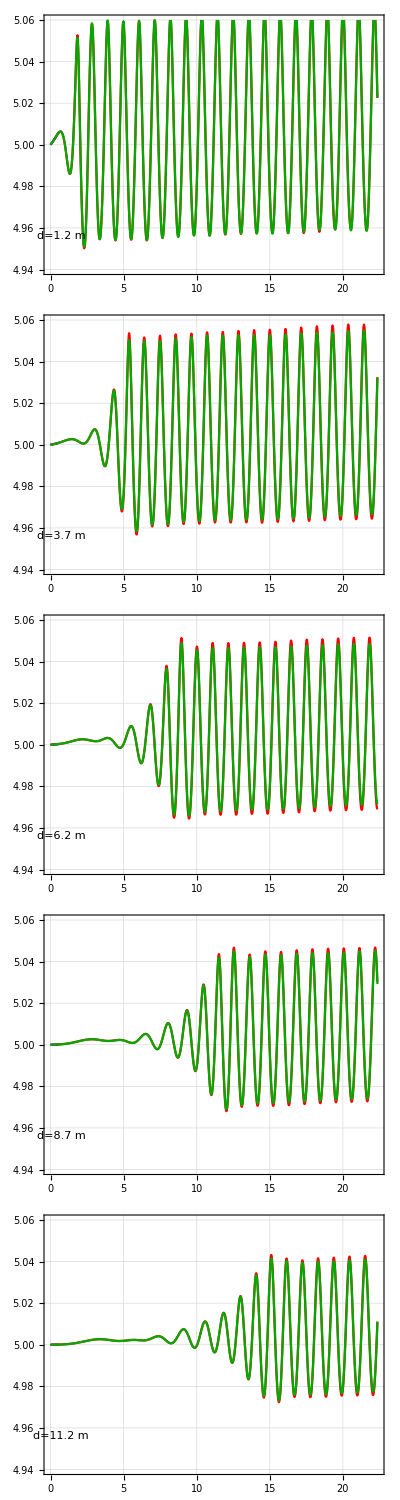
| 
-Graphics-Time [s]Surface Elevation [m] |

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/mesh_quality_ELEMlinear_ALElinear_H0d1.png

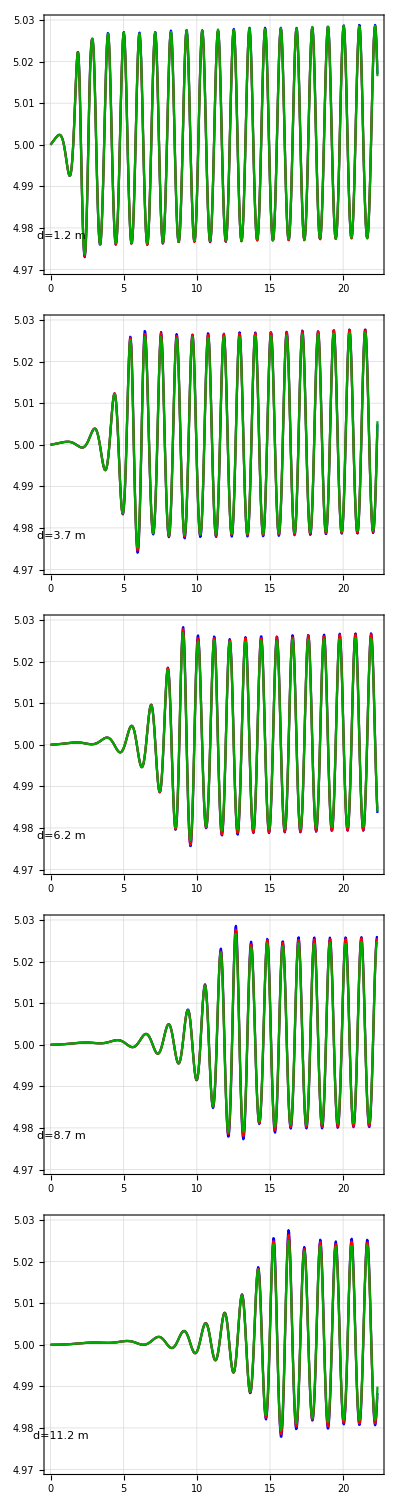
| 
-Graphics-Time [s]Surface Elevation [m] |

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/mesh_quality_ELEMlinear_ALElinear_H0d05.png

ALEの頻度を1/3にすると，波の減衰が大幅に抑えられた．

```mathematica
zrange={-0.06,0.06};
{start,end}={0.,17.+T*5};

ALE="linear";
(*comp0d07={fileName[{0.1,1.8,"potential","water_no_float0d07",0.05,"linear",ALE}],
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};
*)
comp0d08={
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d06_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1"};
fig=compareSimple[FileNameJoin[{fileDir,#,"result.json"}]&/@comp0d08,zrange]
Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/mesh_quality_ELEMlinear_ALElinear_H0d1.png",fig,ImageResolution->300]

comp0d08={
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d06_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1"};

fig=compareSimple[FileNameJoin[{fileDir,#,"result.json"}]&/@comp0d08,{-0.03,0.03}]

Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/mesh_quality_ELEMlinear_ALElinear_H0d05.png",fig,ImageResolution->300]

Text["ALEの頻度を1/3にすると，波の減衰が大幅に抑えられた．"]
```

#### 減衰へのALE頻度の影響 ALE:linear

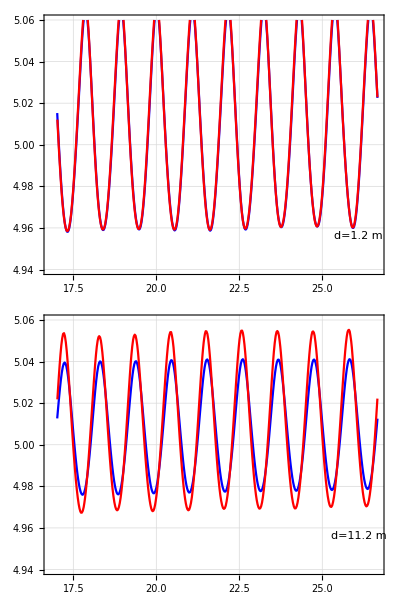
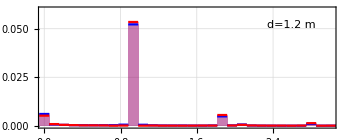
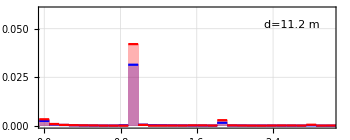
| 
-Graphics-Time [s]Surface Elevation [m] | 
-Graphics--Graphics-Frequency [s^-1]Amplitude.08 [m] |

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/dl0d08_ALE_frequency_comparison.png

ALEの頻度を1/3にすると，波の減衰が大幅に抑えられた．

```mathematica
zrange={-0.03,0.03}*2;
{start,end}={17.,17.+T*9};

ALE="linear";
(*comp0d07={fileName[{0.1,1.8,"potential","water_no_float0d07",0.05,"linear",ALE}],
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};
*)
comp0d08={
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};

fig=compare[FileNameJoin[{fileDir,#,"result.json"}]&/@comp0d08,zrange]

Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/dl0d08_ALE_frequency_comparison.png",fig,ImageResolution->225]

Text["ALEの頻度を1/3にすると，波の減衰が大幅に抑えられた．"]
```

#### 減衰へのALE頻度の影響 ALE:pseudo-quad

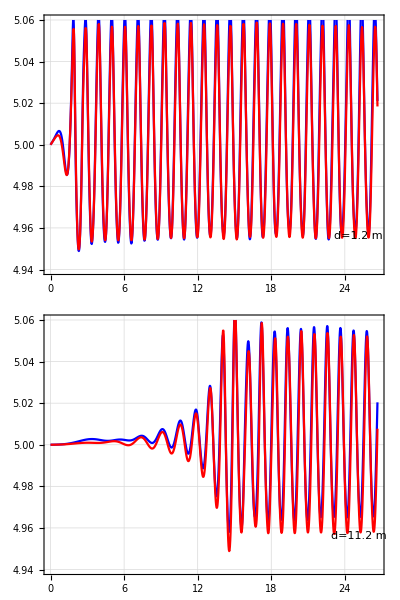
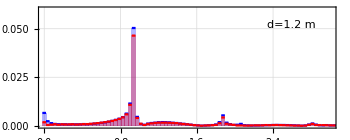
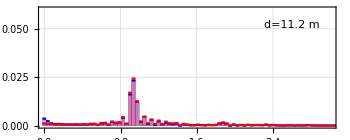
| 
-Graphics-Time [s]Surface Elevation [m] | 
-Graphics--Graphics-Frequency [s^-1]Amplitude.08 [m] |

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/dl0d08_ALE_frequency_pseudo_comparison.png

ALEがpseudoの場合でも頻度を1/3にすると，波の減衰が大幅に抑えられた．ただし，ALEがlinearの場合よりもALE pseudo quadは減衰が生じにくい．

```mathematica
zrange={-0.03,0.03}*2;
{start,end}={0.,17.+T*9};
ALE="pseudo_quad";
(*comp0d07={fileName[{0.1,1.8,"potential","water_no_float0d07",0.05,"linear",ALE}],
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};*)

comp0d08={
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};


fig=compare[FileNameJoin[{fileDir,#,"result.json"}]&/@comp0d08,zrange]

Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/dl0d08_ALE_frequency_pseudo_comparison.png",fig,ImageResolution->225]

Text["ALEがpseudoの場合でも頻度を1/3にすると，波の減衰が大幅に抑えられた．ただし，ALEがlinearの場合よりもALE pseudo quadは減衰が生じにくい．"]
```

#### BVPに擬2次要素を使った場合

{Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1,Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALEpseudo_quad_ALEPERIOD1}

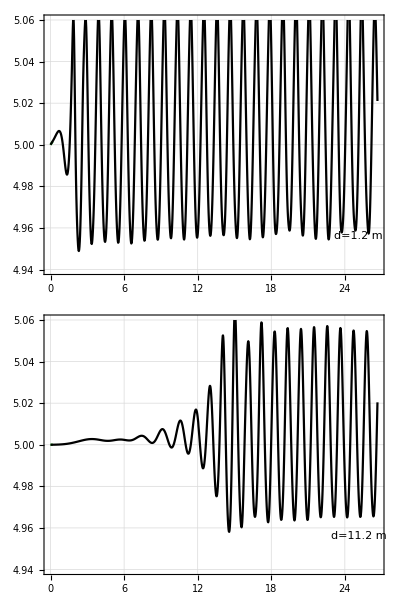
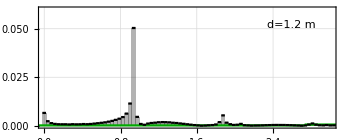
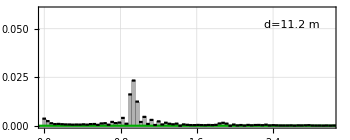
| 
-Graphics-Time [s]Surface Elevation [m] | 
-Graphics--Graphics-Frequency [s^-1]Amplitude.08 [m] |

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/MESH0d08_ELEMpseudo_quad_H0d1.png

ALEを頻繁にメッシュに適用してメッシュを均一にしなければ，pseudo-quadの精度は悪化し，計算が破綻してしまうようだ．
pseudo-quadは，歪なメッシュにおいては計算が不安定になる可能性がある．

```mathematica
zrange={-0.03,0.03}*2.;
colors=RotateLeft[colors,2];
ALE="pseudo_quad";
BVP="linear";
comp={
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMpseudo_quad_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1"}

compare[FileNameJoin[{fileDir,#,"result.json"}]&/@comp,zrange]

Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/MESH0d08_ELEMpseudo_quad_H0d1.png",%,ImageResolution->225]

Text["ALEを頻繁にメッシュに適用してメッシュを均一にしなければ，pseudo-quadの精度は悪化し，計算が破綻してしまうようだ．
pseudo-quadは，歪なメッシュにおいては計算が不安定になる可能性がある．"]
```

#### 最も良いと思われる計算

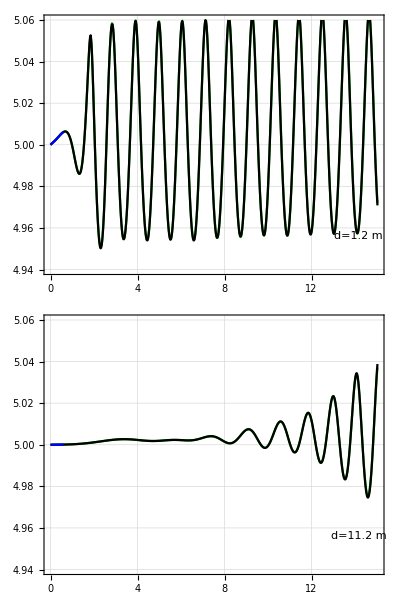
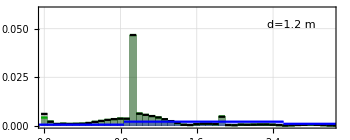
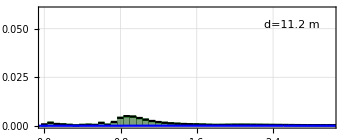
| 
-Graphics-Time [s]Surface Elevation [m] | 
-Graphics--Graphics-Frequency [s^-1]Amplitude.08 [m] |

ALEがpseudoの場合でも頻度を1/3にすると，波の減衰が大幅に抑えられた．ただし，ALEがlinearの場合よりもALE pseudo quadは減衰が生じにくい．

```mathematica
zrange={-0.03,0.03}*2;
{start,end}={0.,T*14};
ALE="pseudo_quad";
fileDir="/Volumes/home/BEM/benchmark202405";
(*comp0d07={fileName[{0.1,1.8,"potential","water_no_float0d07",0.05,"linear",ALE}],
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};*)

comp0d08={
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALElinear_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALElinear_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d06_DT0d05_ELEMlinear_ALElinear_ALEPERIOD1"};


fig=compare[FileNameJoin[{fileDir,#,"result.json"}]&/@comp0d08,zrange]

(*Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/dl0d08_ALE_frequency_pseudo_comparison.png",fig,ImageResolution->225]
*)
Text["ALEがpseudoの場合でも頻度を1/3にすると，波の減衰が大幅に抑えられた．ただし，ALEがlinearの場合よりもALE pseudo quadは減衰が生じにくい．"]
```

{141.12,152.64,190.08,204.48}

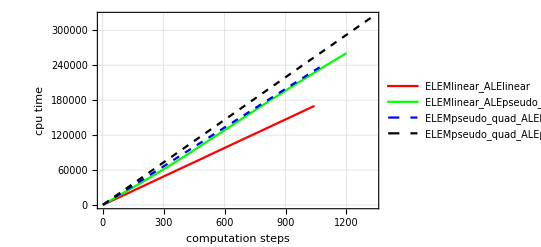

{141.12,152.64,190.08,204.48}

{1.,1.08163,1.34694,1.44898}

```mathematica
list={
"ELEMlinear_ALElinear",
"ELEMlinear_ALEpseudo_quad",
"ELEMpseudo_quad_ALElinear",
"ELEMpseudo_quad_ALEpseudo_quad"};
(*clist={5000,6000,7000,8000}*0.96;*)
clist={4900,5300,6600,7100}*0.96*0.03
Show[ListPlot[
Table[importData["/Volumes/home/BEM/benchmark202404/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_"<>name<>"/result.json","cpu_time"]
(*}*)
,{name,list}]
,FrameLabel->framelabel["computation steps","cpu time"]
,PlotStyle->{Red,{Green},{Blue,Dashed},{Black,Dashed}}
,PlotLegends->list
,GridLines->Automatic
(*,PlotRange->{{0,10},Automatic}*)
,Evaluate[plot2Doption]]
(*,
Plot[Table[c*x,{c,clist}],{x,0,10}]*)
]

clist
clist/clist[[1]]
```